```mathematica
months={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39};
bugs={13,5,10,5,6,8,5,6,7,2,4,3,1,2,1,3,0,0,0,1,0,0,1,3,4,1,0,1,0,1,1,0,0,0,0,0,1,2,0};
data=Thread[{months,Accumulate[bugs]}]
```

{{1,13},{2,18},{3,28},{4,33},{5,39},{6,47},{7,52},{8,58},{9,65},{10,67},{11,71},{12,74},{13,75},{14,77},{15,78},{16,81},{17,81},{18,81},{19,81},{20,82},{21,82},{22,82},{23,83},{24,86},{25,90},{26,91},{27,91},{28,92},{29,92},{30,93},{31,94},{32,94},{33,94},{34,94},{35,94},{36,94},{37,95},{38,97},{39,97}}

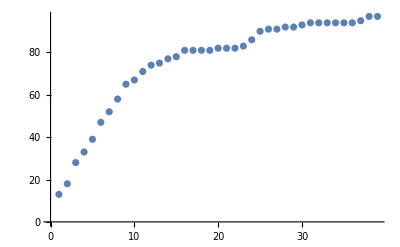

```mathematica
ListPlot[data]
```

```mathematica
shortGoel=NonlinearModelFit[data,a*(1-Exp[-b*t]),{{a,5260},b},t]
```

FittedModel[95.2748 (1-ⅇ^(-0.113746 t))]

```mathematica
shortGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 95.2748 | 0.754345 | 126.301 | 2.27199×10^-50
b | 0.113746 | 0.00313757 | 36.2529 | 1.63539×10^-30

Тъй като стандартната грешка и за двата параметъра е по- малка от estimate, t- статистиката е по- голяма от 2 и p- стойностите са по- малки от 0.05, то параметрите на модела са значими и имаме адекватен апроксимационен модел.

```mathematica
shortGoel["BestFitParameters"]
```

{a→95.2748,b→0.113746}

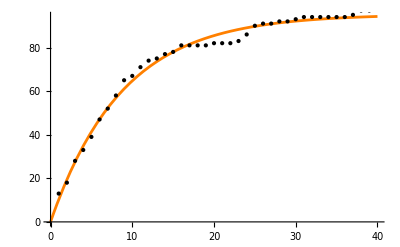

```mathematica
Plot[shortGoel[t],{t,0,40},Epilog->Point[data],PlotStyle->Orange]
```

```mathematica
shortGoel["AIC"]
```

181.36

```mathematica
shortGoel["BIC"]
```

186.351

```mathematica
shortGoel["RSquared"]
```

0.999151

```mathematica
shortGoel["AdjustedRSquared"]
```

0.999105

```mathematica
gompertzMakeham=NonlinearModelFit[data,a*(1-Exp[-λ*t-(α/β)*(Exp[β*t]-1)]),{{a,100},{α,0.75},{β,0.45},{λ,0.05}},t,PrecisionGoal->Infinity,MaxIterations->Infinity]
```

FittedModel[101.898 (1-ⅇ^(3.13261 (-1+ⅇ^(-0.0327955 t))-0.0131924 t))]

```mathematica
gompertzMakeham["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 101.898 | 1271.21 | 0.0801582 | 0.936568
α | 0.102736 | 15.521 | 0.00661914 | 0.994756
β | -0.0327955 | 3.79688 | -0.00863749 | 0.993157
λ | 0.0131924 | 16.9746 | 0.000777184 | 0.999384

Тъй като стандартната грешка за параметрите a,α,λ е по- малка от estimate, t- статистиката е по- голяма от 2 и p- стойностите са по- малки от 0.05, приемаме, че тези параметри са значими за модела.  β параметърът не покрива тези изисквания следователно, той е незначим за нашия модел.

```mathematica
gompertzMakeham["BestFitParameters"]
```

{a→101.898,α→0.102736,β→-0.0327955,λ→0.0131924}

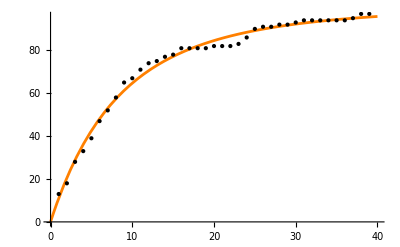

```mathematica
Plot[gompertzMakeham[t],{t,0,40},Epilog->Point[data],PlotStyle->Orange]
```

```mathematica
gompertzMakeham["AIC"]
```

179.9

```mathematica
gompertzMakeham["BIC"]
```

188.218

```mathematica
gompertzMakeham["RSquared"]
```

0.999265

```mathematica
gompertzMakeham["AdjustedRSquared"]
```

0.999181

```mathematica
ZhangTengPhamModel=NonlinearModelFit[data,a/(p-β)*(1-((1+α)*Exp[-b t])/(1+α*Exp[-b t]))^(c/b(p-β)),{{a,97},{α,-0.1},p,b,c,{β,0.2}},t,PrecisionGoal->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[150.73 (1+(0.320359 ⅇ^(«21» t))/(1-1.32036 ⅇ^(«1»)))^1.44363]

```mathematica
ZhangTengPhamModel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 61.9768 | 0.000782912 | 79161.9 | 3.49818×10^-138
α | -1.32036 | 0.380542 | -3.46968 | 0.00147214
p | 0.805329 | 0.0600982 | 13.4002 | 6.69298×10^-15
b | -0.0520759 | 0.0316472 | -1.64551 | 0.109357
c | -0.182836 | 0.133246 | -1.37217 | 0.179267
β | 0.39415 | 0.0600982 | 6.55844 | 1.88272×10^-7

Тъй като стандартната грешка за всички параметъри е по- малка от estimate, t- статистиката е по- голяма от 2 и p- стойностите са по- малки от 0.05, то параметрите на модела са значими и имаме адекватен апроксимационен модел.

```mathematica
ZhangTengPhamModel["BestFitParameters"]
```

{a→61.9768,α→-1.32036,p→0.805329,b→-0.0520759,c→-0.182836,β→0.39415}

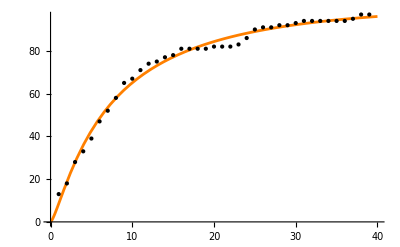

```mathematica
Plot[ZhangTengPhamModel[t],{t,0,40},Epilog->Point[data],PlotStyle->Orange]
```

```mathematica
ZhangTengPhamModel["AIC"]
```

182.915

```mathematica
ZhangTengPhamModel["BIC"]
```

194.56

```mathematica
ZhangTengPhamModel["RSquared"]
```

0.999289

```mathematica
ZhangTengPhamModel["AdjustedRSquared"]
```

0.999159

```mathematica
musaOkumoto= NonlinearModelFit[data,a*(Log[1+b*t]),{{a,97},b},t]
```

FittedModel[30.2028 Log[1+0.693373 t]]

```mathematica
musaOkumoto["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 30.2028 | 1.44852 | 20.8508 | 4.78259×10^-22
b | 0.693373 | 0.096562 | 7.1806 | 1.63093×10^-8

Тъй като стандартната грешка и за двата параметъра е по- малка от estimate, t- статистиката е по- голяма от 2 и p- стойностите са по- малки от 0.05, то параметрите на модела са значими.

```mathematica
musaOkumoto["BestFitParameters"]
```

{a→30.2028,b→0.693373}

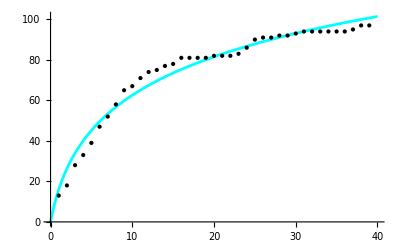

```mathematica
Plot[musaOkumoto[t],{t,0,40},Epilog->Point[data],PlotStyle->Cyan]
```

```mathematica
musaOkumoto["AIC"]
```

221.785

```mathematica
musaOkumoto["BIC"]
```

226.776

```mathematica
musaOkumoto["RSquared"]
```

0.997605

```mathematica
musaOkumoto["AdjustedRSquared"]
```

0.997476

```mathematica
YamadaExp=NonlinearModelFit[data,a*(1-Exp[-r*α*(1-Exp[-β*t])]),{{a,100},r,{α,0.1},{β,0.1}},t]
```

FittedModel[102.303 (1-ⅇ^(-4.0355 (1-ⅇ^(-0.0285099 t))))]

```mathematica
YamadaExp["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 102.303 | 7.98924 | 12.8051 | 9.09396×10^-15
r | 6.57942 | 0.0435874 | 150.948 | 7.54617×10^-51
α | 0.613352 | 0.467562 | 1.31181 | 0.198124
β | 0.0285099 | 0.0209518 | 1.36073 | 0.182297

```mathematica
YamadaExp["BestFitParameters"]
```

{a→102.303,r→6.57942,α→0.613352,β→0.0285099}

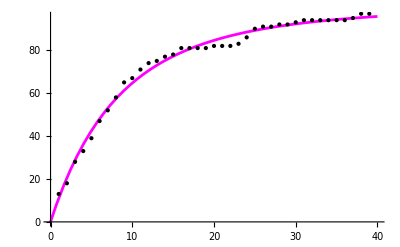

```mathematica
Plot[YamadaExp[t],{t,0,40},Epilog->Point[data],PlotStyle->Magenta]
```

```mathematica
YamadaExp["AIC"]
```

179.932

```mathematica
YamadaExp["BIC"]
```

188.249

```mathematica
YamadaExp["RSquared"]
```

0.999264

```mathematica
YamadaExp["AdjustedRSquared"]
```

0.99918

```mathematica
modelPham=NonlinearModelFit[data,a*(1-(β/(β-1+a^{t^b}))^α),{{a,100},b,{α,0.1},β},t]
```

FittedModel[97.4216 (1-1.04892 (1/(3.28505+(«18»)^(t^(«19»))))^0.0328212)]

```mathematica
modelPham["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 97.4216 | 1.83794 | 53.0058 | 5.07146×10^-35
b | 0.879099 | 0.0880289 | 9.98648 | 8.78352×10^-12
α | 0.0328212 | 0.00738791 | 4.44255 | 0.0000852755
β | 4.28505 | 5.98433 | 0.716046 | 0.478714

Тъй като стандартната грешка за параметрите a,b,α е по- малка от estimate, t- статистиката е по- голяма от 2 и p- стойностите са по- малки от 0.05, приемаме, че тези параметри са значими за модела.  β параметърът не покрива тези изисквания следователно, той е незначим за нашия модел.

```mathematica
modelPham["BestFitParameters"]
```

{a→97.4216,b→0.879099,α→0.0328212,β→4.28505}

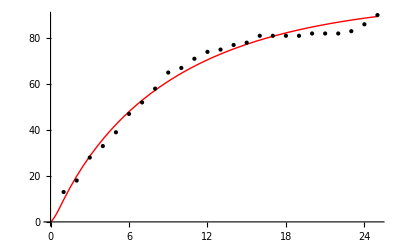

```mathematica
modelPhamPlot=Plot[modelPham[x],{x,0,25},Epilog->Point[data],PlotStyle->{Red,Thick}]
```

```mathematica
modelPham["AIC"]
```

182.936

```mathematica
modelPham["BIC"]
```

191.253

```mathematica
modelPham["RSquared"]
```

0.999205

```mathematica
modelPham["AdjustedRSquared"]
```

0.999115

```mathematica
Grid[{#,shortGoel[#],gompertzMakeham[#],ZhangTengPhamModel[#],musaOkumoto[#],YamadaExp[#],modelPham[#]}& [{"AIC","BIC","RSquared","AdjustedRSquared"}],Alignment->Center,Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
181.36 | 186.351 | 0.999151 | 0.999105
179.9 | 188.218 | 0.999265 | 0.999181
182.915 | 194.56 | 0.999289 | 0.999159
221.785 | 226.776 | 0.997605 | 0.997476
179.932 | 188.249 | 0.999264 | 0.99918
182.936 | 191.253 | 0.999205 | 0.999115

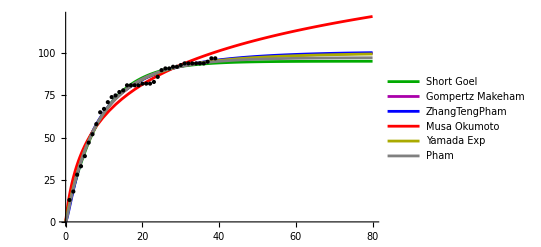

```mathematica
Plot[{shortGoel[x],gompertzMakeham[x],ZhangTengPhamModel[x],musaOkumoto[x],YamadaExp[x],modelPham[x]},{x,0,80},PlotRange->All,Epilog->Point[data],
PlotStyle->{Darker[Green],Darker[Magenta],Blue,Red,Darker[Yellow],Gray},PlotLegends->Placed[{Style["Short Goel",Bold,10],Style["Gompertz Makeham",Bold,10],Style["ZhangTengPham",Bold,10],Style["Musa Okumoto",Bold,10],Style["Yamada Exp",Bold,10],Style["Pham",Bold,10]},{0.75,0.40}]]
```

```mathematica
predictionShort=Table[{i,Round[gompertzMakeham[i]]},{i,40,80}]
```

{{40,96},{41,96},{42,96},{43,96},{44,97},{45,97},{46,97},{47,97},{48,97},{49,98},{50,98},{51,98},{52,98},{53,98},{54,98},{55,98},{56,98},{57,99},{58,99},{59,99},{60,99},{61,99},{62,99},{63,99},{64,99},{65,99},{66,99},{67,99},{68,99},{69,99},{70,99},{71,100},{72,100},{73,100},{74,100},{75,100},{76,100},{77,100},{78,100},{79,100},{80,100}}

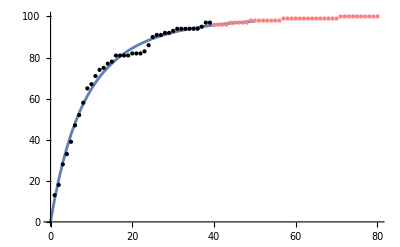

```mathematica
Show[Plot[gompertzMakeham[x],{x,0,50},Epilog->Point[data],PlotRange->All],
ListPlot[predictionShort,PlotStyle->{Pink,PointSize[Medium]},PlotRange->All]]
```